# Clustering with Monadic Memory

Peter Overmann 
15 Aug 2022

This notebook demonstrates how to use Monadic Memory for clustering/pooling a large number of SDRs.

### Monadic Memory Algorithm

```mathematica
MonadicMemory[f_Symbol, {n_Integer, p_Integer}] := Module[  {overlap, D1, D2, items = 0},

DyadicMemory[ D1, {n,p}];
DyadicMemory[ D2, {n,p}];

overlap[a_SparseArray,b_SparseArray]:=Total[BitAnd[a,b]];

(* random SDR *)
f[] := SparseArray[  RandomSample[ Range[n], p]-> Table[1, p], {n}];

(* store and recall x *)
f[x_SparseArray] := Module[ {r,hidden},

r  = D2[D1[D2[D1[x]]]];

If[HammingDistance[x,r]<p,Return[r]];

items++;
hidden = f[];
D1[ x-> hidden]; D2[ hidden-> x]; 

x
];

f["Items"] := items;
]
```

### Noise

Adding salt or pepper noise to an SDR.

```mathematica
SDRNoise[x_SparseArray, bits_Integer] := Module[ {p},

If[bits ≥ 0, 
(* salt noise, adding bits *)
p = Union[Flatten[x["NonzeroPositions"]],  Table[  RandomInteger[{1,Length[x]}], bits]];
SparseArray[ p -> Table[1, Length[p]], {Length[x]} ],

(* pepper noise, removing bits *)
p = Most[ArrayRules[x]];
SparseArray[ RandomSample[ p,  Length[p] + bits], Length[x]]
]
]
```

### Visualization

Plot an SDR  as a square image, padding with zeros if necessary.

```mathematica
SDRPlot[ x_SparseArray ]:= 
Module[ {w, d}, 
w = Ceiling[Sqrt[Length[x]]];
d = Partition[PadRight[Normal[x], w^2], {w}] /. {1-> {0.04,0.18,0.42}, 0-> {0.79,0.86,1.0}};
Image[d, ImageSize-> 2*w]
]
```

### Configuration

```mathematica
Get[  $UserBaseDirectory <> "/TriadicMemory/dyadicmemoryC.m"]
```

```mathematica
n = 1000;
p = 20;
```

```mathematica
MonadicMemory[ M, {n,p}];
```

### Generate Test Data

Generate k=100 random SDRs (“classes”)

```mathematica
k = 100;
```

```mathematica
classes = Table[ M[], k];
```

For each class, make 1000 variations with 4 random bits changed

```mathematica
data = RandomSample[ Flatten[ Table[ SDRNoise[ SDRNoise[#,-4],4], 1000] & /@ classes, 1]];
```

```mathematica
pos[x_SparseArray] := Sort[Flatten[x["NonzeroPositions"]]];
```

```mathematica
Export["data.tsv", pos/@ data];
```

Visualize the distribution of SDR bits in the dataset:

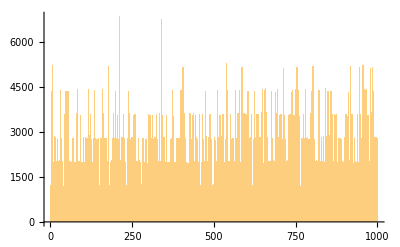

```mathematica
Histogram[ Flatten[Flatten[#["NonzeroPositions"]] & /@ data], n, PlotRange-> All]
```

### Write data set to a Monadic Memory

```mathematica
M /@ data; // AbsoluteTiming
```

{155.345,Null}

Number of hidden vectors created in the Monadic Memory (slightly more than the number of classes)

```mathematica
M["Items"]
```

105

### Write dataset again

```mathematica
out = M /@ data; // AbsoluteTiming
```

{144.324,Null}

The number of stored items has slightly increased (the algorithm keeps learning during recall)

```mathematica
M["Items"]
```

106

Number of recalled items (same as length of dataset)

```mathematica
Length[out]
```

100000

Number of different items in output -- this is the number of clusters found. Each SDR from the original dataset has been mapped to a representative SDR from one of the clusters found.

```mathematica
Union[pos /@ out] // Length
```

111